# SurfCalc for extracting Ball Datum plane and FID plane equations.

PZ Takacs

## SurfCalc OGP_MF03 BallDatum&Fid.nb

## Extracted from SurfAnal10b

2015.02.25 - Fixed cDATUM eqn output to file.
2015.02.24 - Renamed from “SurfCalc OGP_MF03 commission.nb” to reflect the purpose of the code.

2015.02.13 - Added section to input datum plane cal file equations for several runs and plot them versus the mean datum plane.

2014.12.12 - from SurfCalc OGP_CCDonMF01 ver4.nb. Customized for commissioning the MF03 holddown fixture. Added ball sphere fitting section.

Requires that the fixture be mounted on the OGP machine with the 2 LL and LR balls along the front edge and the single UC ball at the rear. The origin of the coordinate system is set to the scribe marks on the front (larger) fiducial surface in the LL corner. The x-axis angle is set with the scribe mark on the right side of the front fiducial surface. All measurements are made relative to this system.

Eventually the ball centers will define the datums.

```mathematica
Button["Run Initialization first",SetOptions[Button,Background->LightOrange];FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

Run Initialization first

## 1. Initialize

```mathematica
SetOptions[Button,Background->LightOrange];
```

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

qqi9w_shm15FrontEndObject[LinkObject["qqi9w_shm", 3, 1]]15SurfCalc OGP_MF03 BallDatum&Fid cal.nb/Users/takacs/ Peter work f/Projects/LSST project/Analysis codes/SurfCalc OGP_MF03 BallDatum&Fid cal.nb

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

Tue 7 Apr 2015 19:21:09

```mathematica
hms$:=DateString[{"Hour","Minute","Second"}]
```

```mathematica
Off[General::"spell1"]
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

```mathematica
TS[x_]:=ToString[x]
```

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

## 1.1. Define statistical functions for profile data. (Inactive)

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

{396.,69.2929,18.8168,9.62957,6.64709,5.6137}

```mathematica
nPts
```

11

```mathematica
Length[psd2side]
```

11

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

√(-(1. worklist^2)/nbefore^2+(2.+worklist)/nbefore)

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

{FontFamily→Arial,FontSize→10}

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

PlotLabel

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

## 2. Enter full file path here to set working directory:

Enter the filepath for a file in each of the data directories, then copy the desired path into the filepathfull expression.

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/MF03 cal runs 150204/MF03 cal run1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work/MF03 141212 ballsand surfs.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/MF03 cal run3.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150220/MF03 150220 LP ball cal run01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150224/MF03CalRun01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/ECM raft#1/ECM#1MF03calfile.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs/ECM#1MF03calfile11.DAT"
```

## 1.0 Execute following after setting the proper file path.

```mathematica
filepathfull = "/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs/ECM#1MF03calfile11.DAT";
```

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"];
```

```mathematica
manualcalcFlag=False; (*set for automated analysis*)
```

```mathematica
manualcalcFlag=True; (*to stop automated analysis with default parameters*)
```

## 2.1 Ball locations from OGP printout. Global coords where x-y origin is from the initialization results.

```mathematica
Input["Abort at interrupt to bypass this section to allow for nominal ball center coords in MF03 coord system. Execute 2.2 to set the coords and compute the raft corner locations."]
Interrupt[]
```

$Aborted

Execute one of these cells to set the approx ball centers.

ballLL = {109.68021, 47.37074, -29.36903, 8.03260/2}; ballLR = {196.16174, 46.89109, -29.39688, 8.02161/2};
ballUC = {153.62359, 160.61988, -29.35125, 8.01668/2};

(* for 141231 data *)
ballLL = {14.37264, 41.5273, -29.40122, 4.00253}; ballLR = {100.87930, 41.62255, -29.37040, 3.92891};
ballUC = {57.49383, 155.05464, -029.51954, 4.13259};

62 Sphere            +014.37461   +041.52476  -029.37916  +004.00129  43 40 44.

  63 Sphere            +100.88601   +041.62049  -029.34504  +003.92382  52 48 54.

  64 Sphere            +057.52614   +155.06837  -029.48253  +004.10302  61 56 57.

ECM#2 data 4 Feb 2015

150220 Ball Fid cal.txt
OGP MM computes sphere center cords and radius
31	Sphere	+014.37204	+041.52050	-029.40110	+004.01866
32	Sphere	+100.85857	+041.61607	-029.42182	+004.00100
33	Sphere	+057.56664	+155.05976	-029.40268	+004.01958

Enter the ball cal file that was Print/Saved from the OGP run. Need to extract the lines that contail the ball fit coords. This differs for each file.

#### Input MM Ball fit coord text file. Compute raft corner points relative to the LL bal center.

#### Need to redo this. Skip it.

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/MF03 cal runs 150204/MF03 cal run1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/MF03 cal runs 150204/MF03 cal run1.DAT"
```

```mathematica
ballfile=Input["Enter path to MM BallFitResult file",ballfile]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Runs 150224/Run2.txt

```mathematica
balldata=Import[ballfile,"List"];
```

```mathematica
balldata[[12;;16]]
```

{   8 Contour           +112.12757   -002.22196  -000.04918  +231.58081 ,   9 Point             +104.27024   -002.84040  -000.04359             ,  10 Contour           +104.59985   -002.92252  -000.04385  +002.05568 ,  11 Point             +008.24165   +197.79181  +000.02935             ,  12 Contour           +008.56285   +197.71141  +000.02937  +002.03507 }

```mathematica
ballLL=ImportString[balldata[[12]],"Words"]//ToExpression;ballLR=ImportString[balldata[[14]],"Words"]//ToExpression;ballUC=ImportString[balldata[[16]],"Words"]//ToExpression;
```

```mathematica
ballsOGPMM={ballLL[[1;;3]],ballLR[[1;;3]],ballUC[[1;;3]]}
```

{{8,Contour,112.128},{10,Contour,104.6},{12,Contour,8.56285}}

```mathematica
ballLL
ballLR
ballUC
```

{8,Contour,112.128,-2.22196,-0.04918,231.581}

{10,Contour,104.6,-2.92252,-0.04385,2.05568}

{12,Contour,8.56285,197.711,0.02937,2.03507}

Read from Print txt file output for 150224 data. Need to have at least one manual text Print file that has the 3 Sphere fits at the end as the last 3 entries. A default is given for the 150224 runs.

```mathematica
ballfile=Input["Enter path to MM BallFitResult file","/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Raft runs 150204-05/ECMraft#2run4list.txt"]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM raft #2/Raft runs 150204-05/ECMraft#2run4list.txt

```mathematica
balldata=Import[ballfile,"List"];
```

```mathematica
sphdata=balldata[[-4;;-2]]
```

{  61 Contour           +057.98793   +156.15350  -025.55169  +008.76028 ,  62 Sphere            +014.37461   +041.52476  -029.37916  +004.00129  43 40 44.,  63 Sphere            +100.88601   +041.62049  -029.34504  +003.92382  52 48 54.}

```mathematica
ToExpression[ImportString[balldata[[12]],"Words"]][[3;;5]]
```

{81.5821,-2.26569,-0.02078}

```mathematica
ballLL=ToExpression[ImportString[sphdata[[1]],"Words"]][[3;;5]];ballLR=ToExpression[ImportString[sphdata[[2]],"Words"]][[3;;5]];ballUC=ToExpression[ImportString[sphdata[[3]],"Words"]][[3;;5]];
```

```mathematica
ballsOGPMM={ballLL,ballLR,ballUC};
```

```mathematica
ballcenters=.;Clear[balldatumplaneOGP];
ballCentOGP=.;
```

```mathematica
fitbasis={1,x,y};fitidx="1,1";
fitord$=StringTake[ToString[fitbasis],{2,-2}]
```

1, x, y

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
balldatumplaneOGP[x_,y_]=Fit[ballsOGPMM,fitbasis,{x,y}]
```

-30.7652+0.000357601 x+0.0332541 y

## 2.2 Raft origin relative to nominal local coord of ball centers:

Compute nominal ball locations as offsets from the LL ball center. Use dimensions from raft baseplate drawing LCA-10212.

```mathematica
ballLL={14.372,41.520,-29.40}
ballLR=ballLL+{86.5,0,0}
ballUC=ballLL+{43.25,113.5,0}
raftcorneroffset={(126.5/2)-43.25,6.5,-29.81};
```

{14.372,41.52,-29.4}

{100.872,41.52,-29.4}

{57.622,155.02,-29.4}

```mathematica
ballsOGPMM={ballLL,ballLR,ballUC};
```

```mathematica
raftLL=ballLL-raftcorneroffset
```

{-5.628,35.02,0.41}

```mathematica
raftedge=126.5;
```

```mathematica
xminraft=raftLL[[1]];xmaxraft=raftLL[[1]]+raftedge;
yminraft=raftLL[[2]];ymaxraft=raftLL[[2]]+raftedge;
```

## 3. Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs

```mathematica
datain=.;datain2=.;datainXYZSR=.;skipnum=.;nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
fnames=FileNames["*.DAT"];Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | ECM#1AbsHgt01.DAT
2 | ECM#1AbsHgt02.DAT
3 | ECM#1AbsHgt03.DAT
4 | ECM#1Flatness01.DAT
5 | ECM#1MF03calfile02.DAT
6 | ECM#1MF03calfile03.DAT
7 | ECM#1MF03calfile11.DAT
8 | ECM#1MF03calfile12.DAT
9 | ECM#1MF03calfile13.DAT
10 | ECM#1MF03calfile.DAT
11 | ECM#1RaftFlatness.DAT

#### Pick the OGP file from the list

```mathematica
inst$="OGP"
```

OGP

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
nf=Input["Enter index of file desired",nf]
```

9

```mathematica
1
```

1

```mathematica
fileinfull =fnames[[nf]]
fileinroot=FileBaseName[fileinfull]
fileinS=fileinroot;filein=fileinS;
```

ECM#1MF03calfile13.DAT

ECM#1MF03calfile13

```mathematica
(*Read in raw data here*)
datain=Import[fileinfull,"Data"];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ](* Stop here to execute next expressons individually as needed to clean up data *)
```

```mathematica
datain[[1;;20]]
```

{{C:\DATA\MF03,holddown\MF03cal150220LPFidBalls03.RTN,03/27/2015,17:19:20,3},{Point,1},{-0.0007,-0.001,0.011694,mm},{},{Point,2},{-0.000616,-0.000778,0.012375,mm},{},{Point,3},{0.317133,-0.231614,0.000714,mm},{},{Point,4},{9.27067,-2.841,0.011958,mm},{},{Contour,5},{9.30345,-2.61331,0.012935,mm},{9.28255,-2.61321,0.013614,mm},{9.26075,-2.61331,0.013767,mm},{9.23425,-2.61351,0.013625,mm},{9.19405,-2.61531,0.013957,mm},{9.17565,-2.61811,0.013707,mm}}

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
workdir=filein<>"_files"
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs

ECM#1MF03calfile13_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

New work dir created

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs/ECM#1MF03calfile13_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
Count[datain,{}] (* Counts the number of blank records in the file*)
```

9908

37

```mathematica
datain2=Select[datain,Length[#]>0&];(*Strip out the blank lines*)
```

```mathematica
contourPos=Position[datain2,"Contour",2]
Length[contourPos]
```

{{10,1},{93,1},{846,1},{929,1},{3251,1},{3335,1},{3419,1},{5152,1},{5238,1},{5434,1},{5633,1},{5856,1},{6069,1},{6254,1},{6413,1},{6600,1},{6784,1},{6962,1},{7156,1},{7379,1}}

20

Delete all of the Point points. Find all the locations where Point occurs. Form ppos2 by taking each positin and adding 1 to specify the data point values corresponding to the Point function. THen Delete the point pairs.

```mathematica
pointPos=Position[datain2,"Point",2]
Length[pointPos]
```

{{2,1},{4,1},{6,1},{8,1},{844,1},{3249,1},{3333,1},{3417,1},{5234,1},{5236,1},{6065,1},{6067,1},{6780,1},{6782,1}}

14

```mathematica
ppos=Take[pointPos,All,1]
```

{{2},{4},{6},{8},{844},{3249},{3333},{3417},{5234},{5236},{6065},{6067},{6780},{6782}}

```mathematica
ppos2=Table[{ppos[[i]],ppos[[i]]+1},{i,Length[ppos]}]//Flatten[#,1]&
```

{{2},{3},{4},{5},{6},{7},{8},{9},{844},{845},{3249},{3250},{3333},{3334},{3417},{3418},{5234},{5235},{5236},{5237},{6065},{6066},{6067},{6068},{6780},{6781},{6782},{6783}}

```mathematica
Length[datain2]
```

9871

```mathematica
datain2=Delete[datain2,ppos2];
```

```mathematica
ppos2={};(*Reset the list to blank after the Delete to avoid excess deletion for subsequent pass troughs*)
```

```mathematica
Length[datain2]
```

9843

Remove all of the data points defined by the “Point” identifier.

```mathematica
Length[datain2]
datain2=Select[datain2,NumericQ[#[[1]]]&]; (* Strip out all the lines that don't start with a number *)
Length[datain2]
```

9843

9818

```mathematica
datain2[[1;;10]]//TableForm
```

9.30345 | -2.61331 | 0.012935 | mm
9.28255 | -2.61321 | 0.013614 | mm
9.26075 | -2.61331 | 0.013767 | mm
9.23425 | -2.61351 | 0.013625 | mm
9.19405 | -2.61531 | 0.013957 | mm
9.17565 | -2.61811 | 0.013707 | mm
9.15465 | -2.62301 | 0.013546 | mm
9.13195 | -2.6313 | 0.014273 | mm
9.10195 | -2.6549 | 0.014217 | mm
9.08675 | -2.6666 | 0.013377 | mm

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ]
```

#### All data points are now in one continuous list. All the contours are merged together

#### continue here

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

Convert z-vals to microns:

```mathematica
xunit$="mm";yunit$="mm";(*These are now current units*)
```

```mathematica
zflag=Input["True if leave z-vals in mm",True]
```

True

```mathematica
datain3x[[1]]
If[zflag,zunit$="mm",datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];zunit$="µm"];
datain3x[[1]]
```

{9.30345,-2.61331,0.012935}

{9.30345,-2.61331,0.012935}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
datainXYZS=datain3x;
datainXYZSR=datainXYZS; (* No FID. Copy surface into SR array. *)
```

```mathematica
skipnum=.;cloudXYZ=.
```

```mathematica
cloudXYZ=datainXYZSR;
Dimensions[cloudXYZ]
```

{9818,3}

Range of raw z-values:

```mathematica
{Min[cloudXYZ[[All,{3}]]],Max[cloudXYZ[[All,{3}]]]}
```

{-25.9197,0.043473}

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from cloudXYZ based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the cloudXYZ as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[cloudXYZ,All,{1}]//Flatten;
yvals=Take[cloudXYZ,All,{2}]//Flatten;
zvals=Take[cloudXYZ,All,{3}]//Flatten;
```

```mathematica
{xmin=Min[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],zmax=Max[zvals],Mean[zvals],StandardDeviation[zvals]}//N
```

{3.18925,112.128}

{-3.26299,198.512}

{-25.9197,0.043473,-12.011,12.7685}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{108.939,201.775,25.9632}

```mathematica
rowscols$="cloud" (*"sparse"*)
```

cloud

Next expression may not contain desired array on first pass. Why???? BEWARE

```mathematica
vp={0,0,Infinity};
Dynamic[vp];
```

```mathematica
Dimensions[cloudXYZ]
```

{9818,3}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
lpp01=ListPointPlot3D[cloudXYZ,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw data"]
```

-Graphics3D-

```mathematica
Button["Export raw data SUT&FID plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_"<>hms$<>"_SUTandFIDraw.tiff",lpp01,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export raw data SUT&FID plot

#### Separate FID from 3 ball region. Then isolate each ball region. Use global coord system, not part local.

```mathematica
xyrange={{xmin,xmax},{ymin+25,ymax-25}}
```

{{3.18925,112.128},{21.737,173.512}}

```mathematica
{{imin,imax},{jmin,jmax}}=xyrange;
```

```mathematica
xminBalls=imin;xmaxBalls=imax;yminBalls=jmin;ymaxBalls=jmax;
```

```mathematica
{{xminBalls,xmaxBalls},{yminBalls,ymaxBalls}}//MatrixForm
```

(3.18925 | 112.128
21.737 | 173.512)

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

### Now separate the point cloud into 2 regions: SUT and FID

## 4. Work on FID region. Do plane fit and toss out bad points. Iterate if necessary.

#### Define FID region: Exclude points outside of central x-region and outside of y-limits.

```mathematica
FIDdata=.;testR=.;rplt=.;histresidplt=.;
```

```mathematica
testR =Reap[ Do[If[
(cloudXYZ[[i]][[1]]<xmaxBalls&& cloudXYZ[[i]][[1]]>xminBalls)&&
(cloudXYZ[[i]][[2]]>ymaxBalls|| cloudXYZ[[i]][[2]]<yminBalls)

,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
```

```mathematica
FIDdata=Drop[testR,1]//Flatten[#,2]&;
```

```mathematica
Length[FIDdata]
```

5206

#### Restart here for FID iteration bad point cleanup

```mathematica
If[Length[FIDdata]==0,MessageDialog["Setting FID to const plane"];zSUTconst=Mean[SUTdata[[All,3]]];FIDdata=Table[{SUTdata[[i,1]],SUTdata[[i,2]],zSUTconst},{i,Length[SUTdata]}]];
```

```mathematica
rplt=ListPointPlot3D[FIDdata,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw FID data"]
```

-Graphics3D-

```mathematica
Button["Output FID region points plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_FIDpts.tiff",rplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output FID region points plot

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Look at FID data

```mathematica
test=.;zFIDdata=.;
```

```mathematica
zFIDdata=Take[FIDdata,All,{3}]//Flatten;
```

```mathematica
maxzR=Max[zFIDdata];minzR=Min[zFIDdata];sigmaR=StandardDeviation[zFIDdata];
zbinR=BinCounts[zFIDdata,(maxzR-minzR)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeR99=hrange[zFIDdata,0.005,0.995];
PVrangeR99=hgtrangeR99[[2]]-hgtrangeR99[[1]];
sigmaR//NumberForm[#,5]&
```

0.028376

```mathematica
histresidplt=Histogram[zFIDdata,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>"\n99% range="<>ToString[hrange[zFIDdata,0.005,0.995]//NumberForm[#,5]&]<>" PV99="<>ToString[PVrangeR99]<>"\nsdev="<>ToString[sigmaR//NumberForm[#,5]&]<>zunit$];
```

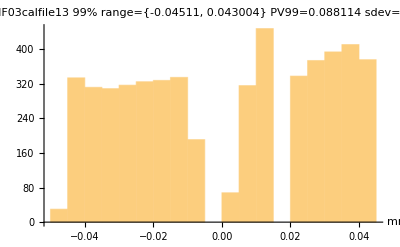

```mathematica
{histresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Now fit a plane surface to the FID points

```mathematica
fitbasisR={1,x,y};fitidxR="1,1";
fitordR$=StringTake[ToString[fitbasisR],{2,-2}]
```

1, x, y

```mathematica
cFID[x_,y_]=Fit[FIDdata,fitbasisR,{x,y}]
```

0.0221921-0.000579449 x+0.000126241 y

```mathematica
vp1={-5,-10,10}
```

{-5,-10,10}

```mathematica
refplt=Plot3D[cFID[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},AxesLabel->{"Xval","Yval",""},ColorFunction->"Rainbow",ImageSize->200,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
FIDresids=Table[{FIDdata[[i,1]],FIDdata[[i,2]],FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]}
,{i,1,Length[FIDdata]}
];
```

```mathematica
reflen$=ToString[Length[FIDresids]]
```

5206

```mathematica
FIDresidsPlt=ListPointPlot3D[FIDresids,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval","Z[µm]"},PlotLabel->fileinS<>"\nThis shows FID after subt plane fit"]
```

-Graphics3D-

```mathematica
Button["Export FIDresids plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDresids.tiff",FIDresidsPlt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export FIDresids plot

```mathematica
zFIDresids=Take[FIDresids,All,{3}]//Flatten;
```

```mathematica
Show[refplt,rplt]
```

-Graphics3D-

Look at quality of FID plane correction to FID points:

Look at quality of FID plane correction to FID points:

```mathematica
maxzR2=Max[zFIDresids];minzR2=Min[zFIDresids];sigmaR2=StandardDeviation[zFIDresids];
zbinR2=BinCounts[zFIDresids,(maxzR2-minzR2)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrange99=hrange[zFIDresids,0.005,0.995];
PVrange99=hgtrange99[[2]]-hgtrange99[[1]];skewR2=Skewness[zFIDresids];
kurtR2=Kurtosis[zFIDresids];
sigmaR2//NumberForm[#,5]&
```

0.0012309

```mathematica
histFIDresidplt=Histogram[zFIDresids,50,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>" FIDresids"<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$<>", skew= "<>TS[skewR2//NumberForm[#,4]&]<>", kurt= "<>TS[kurtR2//NumberForm[#,4]&]

];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

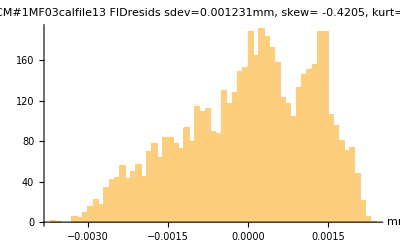

```mathematica
{histFIDresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
Button["Export FID resids histogram plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDhist.tiff",histFIDresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export FID resids histogram plot

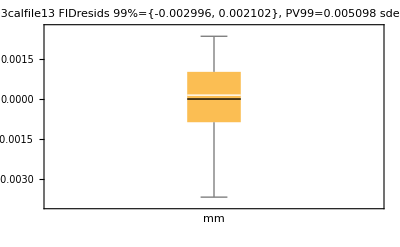

```mathematica
rbwc=BoxWhiskerChart[zFIDresids,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>" FIDresids"<>"\n99%="<>ToString[hrange[zFIDresids,0.005,0.995]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrange99//NumberForm[#,4]&]<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export FID box whisker chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDboxwhisk.tiff",rbwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export FID box whisker chart file

Trim both the XYZ and the Z data lists

```mathematica
{threshFmin,threshFmax}=Input["Enter {min,max} threshold values for trimming bad FID points.",Quantile[zFIDresids,{0.001,0.999}]]
```

{-0.00323111,0.00221117}

```mathematica
FIDresidsZtrim=
Drop[
Reap[ 
Do[
If[
FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]<threshFmax && FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]>threshFmin,
Sow[FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]] ]]
],
{i,Length[FIDdata]}
]
],
1]//Flatten[#,2]&;
```

```mathematica
FIDdatatrim=
Drop[
Reap[
 Do[
If[
FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]<threshFmax && FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]>threshFmin,Sow[FIDdata[[i]]]
],
{i,Length[FIDdata]}]
],
1]//Flatten[#,2]&;
```

```mathematica
FIDresidsXYZtrim=Table[{FIDdatatrim[[i,1]],FIDdatatrim[[i,2]],FIDresidsZtrim[[i]]},{i,Length[FIDdatatrim]}];
```

```mathematica
maxzFID=Max[FIDresidsZtrim];minzFID=Min[FIDresidsZtrim];
sigmaFID=StandardDeviation[FIDresidsZtrim];
skewFID=Skewness[FIDresidsZtrim];
kurtFID=Kurtosis[FIDresidsZtrim];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

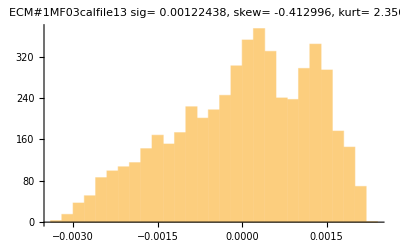

```mathematica
FIDflathist=Histogram[FIDresidsZtrim,5(maxzFID-minzFID)/sigmaFID//Round[#]&,PlotLabel->filein<>"\nsig= "<>TS[sigmaFID]<>", skew= "<>TS[skewFID]<>", kurt= "<>TS[kurtFID]](*These are the residuals after removing plane fit*)
```

Set FIDdata to the trimmed list. Iterate the trim if desired.

```mathematica
cFID[x,y]
```

0.0221921-0.000579449 x+0.000126241 y

```mathematica
FIDdata=FIDdatatrim;
```

```mathematica
Button["Click to iterate FIDdata trim to recalc cFID fit eqn",NotebookLocate["FIDdata iterate restart"]]
```

Click to iterate FIDdata trim to recalc cFID fit eqn

## 5. Now work on 3 ball fits.

#### Separate the regions and plot the points first.

First, separate the 3 ball region from the FID region. Use the y coords.

```mathematica
ballsOGPMM
```

{{14.372,41.52,-29.4},{100.872,41.52,-29.4},{57.622,155.02,-29.4}}

```mathematica
ballregions=Table[ Ball[Drop[ballsOGPMM,None,-1][[i]],4.5],{i,3}]
```

{Ball[{14.372,41.52},4.5],Ball[{100.872,41.52},4.5],Ball[{57.622,155.02},4.5]}

```mathematica
ballregions=Table[ Ball[ballsOGPMM[[i]],4.5],{i,3}]
```

{Ball[{14.372,41.52,-29.4},4.5],Ball[{100.872,41.52,-29.4},4.5],Ball[{57.622,155.02,-29.4},4.5]}

```mathematica
centregions=Table[ Ball[ballsOGPMM[[i]],2.5],{i,3}]
```

{Ball[{14.372,41.52,-29.4},2.5],Ball[{100.872,41.52,-29.4},2.5],Ball[{57.622,155.02,-29.4},2.5]}

Separate data into regions around each ball. blist contains the 3 region lists. Exclude the center point of the ball.

```mathematica
Do[If[i==1,blist={}];
templist={};
Do[
If[RegionMember[ballregions[[i]],cloudXYZ[[j]]]&& !RegionMember[centregions[[i]],cloudXYZ[[j]]],AppendTo[templist,cloudXYZ[[j]]],Null]
,{j,Length[cloudXYZ]}
];
Print[templist//Short];
AppendTo[blist,templist]
,{i,3}]
```

{{14.3602,41.5164,-25.3785},«1644»,{14.3767,41.5355,-25.3796}}

{{100.86,41.5163,-25.4176},«1412»,{100.861,41.5213,-25.4233}}

{{57.6102,155.016,-25.3843},«1548»,{57.6286,155.037,-25.3856}}

#### Start next iteration from here after triming outliers from blist pts.

```mathematica
blist//Short
```

{«1»}

```mathematica
Length[blist[[1]]]
```

1610

```mathematica
testS=.;testR=.;SUTdata=.;FIDdata=.;
```

```mathematica
ballplot[balldata_,ballID$_]:=ListPointPlot3D[balldata,PlotRange->All,ViewPoint->{0,-3,1},ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"X[mm]","Y[mm]","Z[mm]"},PlotLabel->"Ball "<>ballID$]
```

```mathematica
bplt={};
```

```mathematica
bplt=Table[ballplot[blist[[i]],ToString[i]],{i,1,3}];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
allBallptsplot=GraphicsRow[bplt,ImageSize->600]
```

-Graphics-

```mathematica
Button["Output ball point cloud plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_Ballpts1.tiff",allBallptsplot,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output ball point cloud plot

#### Now fit each ball to a sphere and extract the coords.

Fist, express z as a function of the 4 parameters. Solve the canonical equation for z.

```mathematica
RR=.;x0=.;y0=.;z0=.;r0=.;
```

```mathematica
spheqn=(x-x0)^2+(y-y0)^2+(z-z0)^2-r0^2==0;
```

```mathematica
solnz=Solve[spheqn,z];
```

```mathematica
eqnz=z/.solnz[[2]];
```

Function to fit to a ball data input array

```mathematica
nominalR=4.0; (*Need initial guess*)
```

```mathematica
fitballdata[ptclouddata_]:= 
Block[{pts},pts=ptclouddata;pts0=Mean[pts];fitpts=NonlinearModelFit[pts,eqnz,{{x0,pts0[[1]]},{y0,pts0[[2]]},{z0,pts0[[3]]},{r0,nominalR}},{x,y},PrecisionGoal->20,AccuracyGoal->20];fitpts[{"BestFitParameters","ParameterConfidenceIntervalTable"}]//Column]
```

```mathematica
fitballdata[blist[[2]]]
```

{x0→100.948,y0→41.3927,z0→-29.4313,r0→4.015}
 | Estimate | Standard Error | Confidence Interval
x0 | 100.948 | 0.000162938 | {100.948,100.949}
y0 | 41.3927 | 0.000173857 | {41.3924,41.3931}
z0 | -29.4313 | 0.00099115 | {-29.4333,-29.4294}
r0 | 4.015 | 0.000943979 | {4.01315,4.01685}

```mathematica
fitpts["FitResiduals"]//Short
```

{0.00155181,0.0012409,«1379»,-0.00011199}

```mathematica
Do[If[i==1,fitpts=.;fitres1={};fitres2={};fitres22={};fitres23={};fitres24={};fitres3={};fitfcn={};fitfcnpure={};
pts0={};fitzresids={};ballfits={}];


pts0=Mean[blist[[i]]];(*Print[pts0];*)fitpts=NonlinearModelFit[blist[[i]],eqnz,{{x0,pts0[[1]]},{y0,pts0[[2]]},{z0,pts0[[3]]},{r0,nominalR}},{x,y}];
AppendTo[ballfits,{x0,y0,z0,r0}/.fitpts[{"BestFitParameters"}]];{x0,y0,z0,r0}/.fitpts[{"BestFitParameters"}];
Print[{x0,y0,z0,r0}/.fitpts[{"BestFitParameters"}]];
AppendTo[fitzresids,fitpts[{"FitResiduals"}]];AppendTo[fitfcn,fitpts[{"BestFit"}]];
AppendTo[fitfcnpure,fitpts[{"Function"}]];
AppendTo[fitres1,fitpts[{"BestFitParameters"}]];AppendTo[fitres2,fitpts[{"ParameterConfidenceIntervalTable"}]];AppendTo[fitres22,fitpts[{"ParameterErrors"}]];
AppendTo[fitres23,fitpts[{"ParameterTable"}]];AppendTo[fitres24,fitpts[{"ParameterTableEntries"}]];AppendTo[fitres3,fitpts[{"ANOVATable"}]]

,{i,3}]
ballfits=Flatten[ballfits,1];
fitzresids=Flatten[fitzresids,1];
```

{{14.462,41.4949,-29.4008,4.02322}}

{{100.948,41.3927,-29.4313,4.015}}

{{57.9117,154.933,-29.3948,4.02206}}

```mathematica
out$=fileinS<>"\nParameters are {x0,y0,z0,r0}\nNominal OGP values: \n"<>ToString[ballsOGPMM//Column]<>"\n\nFit parameters:\n";
```

```mathematica
{out$,fitres1//Column,fitres2//Column};
```

```mathematica
Button["Output the fit results to PDF",Export[StringTake[fileinS,12]<>"BallFits3.PDF",{out$,fitres1//Column,fitres2//Column}//Column]]
```

Output the fit results to PDF

Look at histogram of residuals of each ball after subtracting best fit sphere. Look for particularly bad fits and then figure out why.

```mathematica
sdev=Map[StandardDeviation,fitzresids]
```

{0.00130281,0.00138238,0.00123866}

```mathematica
kurt=Map[Kurtosis,fitzresids]
```

{2.04889,1.91244,2.27809}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

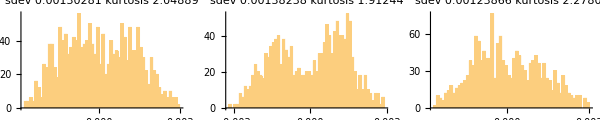

```mathematica
histoplt=GraphicsRow[Table[Histogram[fitzresids[[i]],50,BaseStyle->Directive[FontSize->6,FontFamily->"Arial"],PlotLabel->"sdev "<>TS[sdev[[i]]]<>"\nkurtosis "<>TS[kurt[[i]]]],{i,Length[fitzresids]}],ImageSize->600]
```

```mathematica
Button["Output pt residual histograms",Export[ToString[StringDrop[fileinS,0]]<>"_"<>"_3zreshisto.tiff",histoplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output pt residual histograms

#### This section to trim the ball pts to improve fit. Compute diff between pt and fit surf at pt x,y coords. Save diffs. Compute quantiles on the diffs. Set trim criterion. Trim off the outliers with Sow-Reap, going through the diff calc again.

```mathematica
blistresids={};
Do[
blisttemp={};
Do[fitpt=Apply[fitfcnpure[[j]][[1]],blist[[j,i,1;;2]]];

diffz=blist[[j,i,3]]-fitpt;
AppendTo[blisttemp,diffz]
,{i,1,Length[blist[[j]]]}]
AppendTo[blistresids,blisttemp]
,{j,1,Length[blist]}
]
```

```mathematica
Length[blistresids]
```

3

```mathematica
blistresids[[1,1;;10]]
```

{0.000427771,0.000364267,0.000460243,0.000979356,0.000778819,0.00062422,0.000764287,0.00164378,0.00128543,0.0016467}

```mathematica
Map[Mean,blistresids]
```

{2.44674×10^-14,-1.16278×10^-13,8.04428×10^-11}

```mathematica
{meanB=Map[Mean,blistresids],sdevB=Map[StandardDeviation,blistresids],kurtB=Map[Kurtosis,blistresids]}
```

{{2.44674×10^-14,-1.16278×10^-13,8.04428×10^-11},{0.00130281,0.00138238,0.00123866},{2.04889,1.91244,2.27809}}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

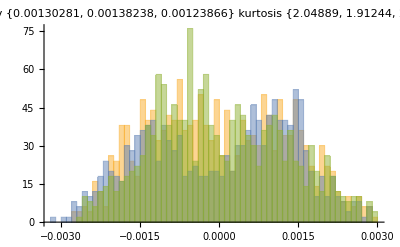

```mathematica
histballs=Histogram[blistresids,50,BaseStyle->Directive[FontSize->6,FontFamily->"Arial"],PlotLabel->"sdev "<>TS[sdevB]<>"\nkurtosis "<>TS[kurtB]]
```

```mathematica
qballs=Map[Quantile[#,{0.01,0.99}]&,blistresids]
```

{{-0.00242375,0.00266731},{-0.00271603,0.00264535},{-0.00247841,0.0026608}}

```mathematica
Button["Output trimmed ball histgram graphics",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_ballhist.tiff",histballs,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output trimmed ball histgram graphics

Now trim the blist pts according to the 1% - 99% range.

```mathematica
blisttrim={};
Do[
blisttemp={};
dropct=0;
Do[fitpt=Apply[fitfcnpure[[j]][[1]],blist[[j,i,1;;2]]];

diffz=blist[[j,i,3]]-fitpt;
If[diffz>qballs[[j,1]]&&diffz<qballs[[j,2]],
AppendTo[blisttemp,blist[[j,i]]],dropct++]
,{i,1,Length[blist[[j]]]}];
Print[{j,dropct}];
AppendTo[blisttrim,blisttemp]
,{j,1,Length[blist]}
];
```

{1,36}

{2,28}

{3,32}

```mathematica
Button["Set blist to the trimmed pts",blist=blisttrim]
```

Set blist to the trimmed pts

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Length[blisttrim[[3]]]
```

1486

```mathematica
Button["Go back to iterate blist fits",NotebookLocate["Iterate blist pts"]]
```

Go back to iterate blist fits

## Compute the difference between the MeasureMind coords and the Mathematica fits to the point clouds. Export the points and the differences to an Excel file.

```mathematica
ballfits
```

{{14.462,41.4949,-29.4008,4.02322},{100.948,41.3927,-29.4313,4.015},{57.9117,154.933,-29.3948,4.02206}}

```mathematica
ballsOGPMM
```

{{14.372,41.52,-29.4},{100.872,41.52,-29.4},{57.622,155.02,-29.4}}

```mathematica
ballcoorddiffs=ballfits[[All,1;;3]]-ballsOGPMM
```

{{0.0900285,-0.0250771,-0.000764138},{0.0762299,-0.127262,-0.0313128},{0.289681,-0.0865436,0.00516123}}

Format the results for output to Excel file.

```mathematica
ballfits
```

{{14.462,41.4949,-29.4008,4.02322},{100.948,41.3927,-29.4313,4.015},{57.9117,154.933,-29.3948,4.02206}}

```mathematica
ballfitresults$="Ball results for data file "<>fileinfull<>"\n\nNominal MF03 ball coords:\n"<>TS[ballsOGPMM//TableForm]<>"\n\nFit results:\n"<>"\tXc\tYc\tZc\tRfit\n"<>TS[ballfits//TableForm]<>"\n\n"<>TS[fitres2//TableForm]
```

Ball results for data file ECM#1MF03calfile13.DAT

Nominal MF03 ball coords:
14.372    41.52    -29.4

100.872   41.52    -29.4

57.622    155.02   -29.4

Fit results:
	Xc	Yc	Zc	Rfit
14.462    41.4949   -29.4008   4.02322

100.948   41.3927   -29.4313   4.015

57.9117   154.933   -29.3948   4.02206

     Estimate   Standard Error   Confidence Interval

                                 14.4617
x0   14.462     0.000142221      14.4623

                                 41.4946
y0   41.4949    0.000146146      41.4952

                                 -29.4025
z0   -29.4008   0.000884882      -29.399

                                 4.02157
r0   4.02322    0.000842343      4.02487

     Estimate   Standard Error   Confidence Interval

                                 100.948
x0   100.948    0.000162938      100.949

                                 41.3924
y0   41.3927    0.000173857      41.3931

                                 -29.4333
z0   -29.4313   0.00099115       -29.4294

                                 4.01315
r0   4.015      0.000943979      4.01685

     Estimate   Standard Error   Confidence Interval

                                 57.9114
x0   57.9117    0.000151255      57.912

                                 154.933
y0   154.933    0.000148293      154.934

                                 -29.3965
z0   -29.3948   0.000843198      -29.3932

                                 4.02048
r0   4.02206    0.000805595      4.02364

```mathematica
Button["Output the full fit results",
Export[filein<>"BallFitResults.txt",ballfitresults$]]
```

Output the full fit results

```mathematica
ballcoorddiffs
```

{{0.0900285,-0.0250771,-0.000764138},{0.0762299,-0.127262,-0.0313128},{0.289681,-0.0865436,0.00516123}}

```mathematica
ballcoorddiffsout=Prepend[ballcoorddiffs,{"x0","y0","z0"}];
ballcoorddiffsout=Prepend[Transpose[ballcoorddiffsout],{"LL","LR","UC"}];
ballcoorddiffsout=Prepend[ballcoorddiffsout,{fileinS<>"\nDifference: SurfCalc - MeasureMind","","",""}];
```

```mathematica
filein
```

ECM#1MF03calfile13

```mathematica
Button["Output the ballcoorddiffs results",
Export[fileinS<>"_BallDiffs.txt",ballcoorddiffsout]]
```

Output the ballcoorddiffs results

#### Plot results

```mathematica
vp1={0,-2,2.0};
```

Define a plot function that will plot any one of the surface fits. Take the center points from the fit centers in fitres1 and set the plot region size with the delta parameter. The ReleaseHold and Hold and Evaluate is necessary to allow the plot range limits to be calculated before the plot is evaluated.

```mathematica
Bfitplt=.;
```

```mathematica
Bfitplt[i_,delta_]:=ReleaseHold@(Hold[Plot3D[fitfcn[[i]],Evaluate[{x,x0-delta,x0+delta}],Evaluate[{y,y0-delta,y0+delta}],ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.3],ViewPoint->Dynamic[vp1]]]//.fitres1[[i,1]])
```

```mathematica
BallandFit[i_]:=Show[Bfitplt[i,3],bplt[[i]],PlotRange->All,ViewPoint->Dynamic[vp1],AxesLabel->{"X[mm]","Y[mm]",""},PlotLabel->fileinS<>"\nSpherical fit to OGP ball points"]
```

```mathematica
BallFitsPts=GraphicsRow[Table[BallandFit[i],{i,3}],ImageSize->600]
```

-Graphics-

```mathematica
Button["Output points and fit graphics",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_Ballpts.tiff",BallFitsPts,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output points and fit graphics

```mathematica
Dynamic[vp1]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Plot FID surface fit with ball fit surfaces.

```mathematica
refplt=Plot3D[cFID[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->200,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]];
```

```mathematica
Show[refplt,BallandFit[1],BallandFit[2],BallandFit[3],PlotRange->All,ImageSize->400,ViewPoint->Dynamic[vp1],AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Compute the cDATUM fit eqn. Then compute the distance of the ball centers from the FID plane. Ball centers define datum plane. First compute datum plane equation from ball centers. THen plot the difference between the 2 planes.

```mathematica
fitbasisR={1,x,y};fitidxR="1,1";
fitordR$=StringTake[ToString[fitbasisR],{2,-2}]
```

1, x, y

```mathematica
(*cDATUM[x_,y_]=balldatumplaneOGP[x,y]*)
```

```mathematica
ballfits
```

{{14.462,41.4949,-29.4008,4.02322},{100.948,41.3927,-29.4313,4.015},{57.9117,154.933,-29.3948,4.02206}}

```mathematica
Clear[cDATUM]
```

```mathematica
cDATUM[x_,y_]=Fit[ballfits[[All,1;;3]],fitbasisR,{x,y}]
```

-29.4034-0.000352998 x+0.000187441 y

```mathematica
Datumplt=Plot3D[cDATUM[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1],AxesLabel->{"X","Y","Z"},PlotLabel->fileinS<>"\ncDATUM plane"]
```

-Graphics3D-

```mathematica
Button["Output cDATUM plot",Export[ToString[StringDrop[fileinS,0]]<>"_cDATUM.tiff",Datumplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output cDATUM plot

```mathematica
vp1
```

{0,-2,2.}

```mathematica
ptsanddatums=Show[Datumplt,BallandFit[1],BallandFit[2],BallandFit[3],PlotLabel->fileinS<>"\nPts & Fit planes",PlotRange->All,ViewPoint->{0,-99,.5}]
```

-Graphics3D-

```mathematica
Button["Output points and fit planes plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_"<>hms$<>"_pts&fitplanes.tiff",ptsanddatums,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output points and fit planes plot

```mathematica
cDATUMFIDdiff[x_,y_]=cDATUM[x,y]-cFID[x,y]
```

-29.4256+0.000226451 x+0.0000611996 y

```mathematica
(cDATUM[x,y]-cFID[x,y])/.x->50/.y->100
```

-29.4082

```mathematica
Plot3D[cDATUM[x,y]-cFID[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.9],AxesLabel->{"Xval","Yval",""},ViewPoint->Dynamic[vp1],PlotLabel->"Difference between Datum and Fiducial planes"]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Add the nominal height of the raft to the ball center z-vals, then fit a plane to these 3 points. This represents the ideal location of the raft relative to the Datum in the MF03 coord system.

```mathematica
nomRaftPts=Map[Apply[Plus,{#,{0,0,29.81}}]&,ballsOGPMM] (*Add the nom raft height value to the z-coords*)
```

{{14.372,41.52,0.41},{100.872,41.52,0.41},{57.622,155.02,0.41}}

```mathematica
nomRaftSurfFit[x_,y_]=Fit[nomRaftPts,{1,x,y},{x,y}]
```

0.41-2.84862×10^-18 x-1.56643×10^-18 y

```mathematica
cDATUM
```

cDATUM

```mathematica
Button["Output the equation results",
Export[StringTake[fileinS,12]<>"DatumEqns.txt",{fileinS<>"\ncDatum[x,y]= "<>ToString[cDATUM[x,y]//InputForm]
<>"\ncFID[x,y] = "<>ToString[cFID[x,y]//InputForm]
<>"\ncDATUMtocFID[x,y] = "<>ToString[cDATUMFIDdiff[x,y]//InputForm]<>"\nnomRaftSurfFit[x,y] = "<>ToString[nomRaftSurfFit[x,y]//InputForm]
}]]
```

Output the equation results

```mathematica
cDATUM[x,y]//StandardForm
```

-29.4034-0.000352998 x+0.000187441 y

```mathematica
cDATUMFIDdiff[x,y]//StandardForm
```

-29.4256+0.000226451 x+0.0000611996 y

DATUM is the surface fit to the 3 ball centers.
FID is the surface fit to the 2 reference flats.
   The coordinate system X,Y origin for all measurements is the global OGP system initialization coordinates. The Z origin is on the top surface of the front fiducial at a specific x,y location.
   The DATUM and FID surfaces are measured during the calibration runs. The plane fit equations to these surfaces are used during the measurement of the raft surface. Need to check to see how repeatable the fit equations are between calibration runs when no changes are made to the location of the fixtures. The raft measurement depends on the calibration surfaces remaining unchanged.
	(cDATUM - cFID) = constant over time.
This difference references the datum surface to the fiducial surface.
   Now measure the raft and the fiducial surface:
	(mRaft - mFID) is the raft surface referenced to the fiducial surface.
   Taking the difference:
	(mRaft - mFID) - (cDATUM - cFID) = mRaft - cDATUM
because this assumes that the fiducial surface fits are the same.
    This last expression defines the absolute raft height relative to the datum plane. The nominal height of the raft above the datum is 29.81mm, so this number can be subtracted from the absolute height to get the residual absolute height error of the raft from the nominal surface plane.

## 6. Lateral ball position distances.

Extract the x,y positons from the ball centers. Compute the distance between the 2 lower balls and the distance from the midpoint between them to the upper ball.

```mathematica
ballsMMxy=Drop[ballsOGPMM,None,-1]
```

{{14.372,41.52},{100.872,41.52},{57.622,155.02}}

```mathematica
MMxdistLLLR=Norm[ballsMMxy[[1]]-ballsMMxy[[2]]];
xmid=(ballsMMxy[[2]]-ballsMMxy[[1]])[[1]]/2;
ymid=(ballsMMxy[[2]]+ballsMMxy[[1]])[[2]]/2;
MMydistUCmid=Norm[ballsMMxy[[3,2]]-{xmid,ymid}[[2]]];
```

```mathematica
Print["MM locs: X dist (86.50) = ",MMxdistLLLR,", Y dist (113.50) = ",MMydistUCmid]
```

MM locs: X dist (86.50) = 86.5, Y dist (113.50) = 113.5

```mathematica
ballsfitxy=Drop[ballfits,None,-2]
```

{{14.4615,41.4946},{100.947,41.3923},{57.911,154.933}}

```mathematica
SCxdistLLLR=Norm[ballsfitxy[[1]]-ballsfitxy[[2]]];
xmid=(ballsfitxy[[2]]-ballsfitxy[[1]])[[1]]/2;
ymid=(ballsfitxy[[2]]+ballsfitxy[[1]])[[2]]/2;
SCydistUCmid=Norm[ballsfitxy[[3,2]]-{xmid,ymid}[[2]]];
```

```mathematica
Print["SurfCalc locs: X dist (86.50) = ",MMxdistLLLR,", Y dist (113.50) = ",SCydistUCmid]
```

SurfCalc locs: X dist (86.50) = 86.5, Y dist (113.50) = 113.49

```mathematica
Button["Output lateral ball separations",
Export[StringTake[fileinS,12]<>"_ballseps.txt",
{fileinS<>"\nMM dist: X dist (86.50) = "<>TS[MMxdistLLLR]<>", Y dist (113.50) = "<>TS[MMydistUCmid]<>"\nSurfCalc dist: X dist (86.50) = "<>TS[MMxdistLLLR]<>", Y dist (113.50) = "<>TS[SCydistUCmid]}]]
```

Output lateral ball separations

## 7. Compare cDATUM - cFID plane equations for several runs repeatability.

Reference the datum plane to the fiducial plane and look at the difference between different runs. Each run consists of switching off the OGP machine, exiting MeasureMind, then restarting the machine and MeasureMind, which causes the OGP to seek home on each axis. Then find and set the SCS origin at the center of the crossed scribe marks. THen run the ball and fiducial surface routine and do the plane fitting above. Reference the datum surface to the FID plane by taking the difference, then compare these difference equations to see how repeatable this process is.

### Input several cDatum equations to plot and compare

```mathematica
MessageDialog["Interrupt will occur to avoid accidental clearing of cdatums. First OK this message, then Abort."]
```

qqi9w_shm42FrontEndObject[LinkObject["qqi9w_shm", 3, 1]]4242

```mathematica
Interrupt[];
```

```mathematica
cdatums={};cfids={};cdatumfids={};
```

Iterate from here:

```mathematica
cdatumfile$=Input["Enter path to cDatum cal planeeqns file",cdatumfile$]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs/ECM#1MF03calfile13_files/ECM#1MF03calDatumEqns.txt

```mathematica
cdatumfile=Import[cdatumfile$,"List"];
```

```mathematica
cdatumfile//TableForm
```

ECM#1MF03calfile13
cDatum[x,y]= -29.40343691318853 - 0.0003529981872446327*x + 0.00018744088825968798*y
cFID[x,y] = 0.022192061667546375 - 0.0005794494370582907*x + 0.00012624124265559551*y
cDATUMtocFID[x,y] = -29.425628974856075 + 0.000226451249813658*x + 0.00006119964560409247*y
nomRaftSurfFit[x,y] = 0.4100000000000005 - 2.8486198647248707*^-18*x - 1.566427318058785*^-18*y

```mathematica
Clear[cdatumeqn,cfideqn]
```

```mathematica
cdatumeqn=cdatumfile[[-4]]//ToExpression
```

-29.4034-0.000352998 x+0.000187441 y

```mathematica
cfideqn=cdatumfile[[-3]]//ToExpression
```

0.0221921-0.000579449 x+0.000126241 y

```mathematica
cDatumToFid=cdatumfile[[-2]]//ToExpression
```

-29.4256+0.000226451 x+0.0000611996 y

```mathematica
AppendTo[cdatums,cdatumeqn];AppendTo[cfids,cfideqn];AppendTo[cdatumfids,cDatumToFid];
```

```mathematica
Length[cdatums]
```

6

```mathematica
meandatums=Mean[cdatums]//Simplify
meanfids=Mean[cfids]//Simplify
meandatumfids=Mean[cdatumfids]//Simplify
```

-29.3979-0.000392441 x+0.000181051 y

0.0229724-0.000577269 x+0.000126425 y

-29.4209+0.000184828 x+0.0000546255 y

```mathematica
cdatumfile$
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs/ECM#1MF03calfile13_files/ECM#1MF03calDatumEqns.txt

```mathematica
topdir=DirectoryName[cdatumfile$,2]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/ECM Raft #1/March15 runs/

```mathematica
parentdirname=FileNameTake[DirectoryName[cdatumfile$,2],-1]
```

March15 runs

```mathematica
vp1={-2,-2,1};
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
ndatum$="_"<>TS[Length[cdatums]]
```

_6

```mathematica
cdatums//TableForm
```

-29.4027-0.000338168 x+0.000196314 y
-29.3938-0.000423658 x+0.000160805 y
-29.3924-0.000432457 x+0.000170067 y
-29.3953-0.000415487 x+0.000187003 y
-29.3999-0.000391876 x+0.000184675 y
-29.4034-0.000352998 x+0.000187441 y

```mathematica
cdatums-meandatums
```

{-0.00477292+0.0000542727 x+0.0000152633 y,0.00413477-0.0000312171 x-0.000020246 y,0.00551879-0.0000400164 x-0.000010984 y,0.00260529-0.0000230463 x+5.95251×10^-6 y,-0.00199561+5.64496×10^-7 x+3.6241×10^-6 y,-0.00549033+0.0000394427 x+6.39005×10^-6 y}

```mathematica
cDatumPlanesPlt=Plot3D[cdatums-meandatums,{x,xminraft,xmaxraft},{y,yminraft,ymaxraft},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.9],AxesLabel->{"X[mm]","Y[mm]",""},ViewPoint->Dynamic[vp1],PlotLabel->ndatum$<>" Datums from "<>TS[parentdirname]<>"\nAvg of"<>ndatum$<>" subt"]
```

-Graphics3D-

```mathematica
Button["Output cDATUM planes plot & mean eqn",SetDirectory[topdir];

Export[parentdirname<>ndatum$<>"_cDATUMplanesAvg_eqn.txt",{parentdirname<>ndatum$<>"_cDATUMplanesAvg_eqn.txt"<>"\ncDatum[x,y]= "<>TS[meandatums//Simplify]}];

Export[parentdirname<>ndatum$<>"_cDATUMplanesAll.tiff",cDatumPlanesPlt,"ImageEncoding"->"LZW",ImageResolution->100];ResetDirectory[],Method->"Queued"]
```

Output cDATUM planes plot & mean eqn

```mathematica
cFidsPlanePlt=Plot3D[cfids-meanfids,{x,xminraft,xmaxraft},{y,yminraft,ymaxraft},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.9],AxesLabel->{"X[mm]","Y[mm]",""},ViewPoint->Dynamic[vp1],PlotLabel->"cFIDs from "<>TS[parentdirname]<>"\nAvg of"<>ndatum$<>" subt"]
```

-Graphics3D-

```mathematica
Button["Output cFID planes plot & mean eqn",SetDirectory[topdir];

Export[parentdirname<>ndatum$<>"_cFIDplanesAvg_eqn.txt",{parentdirname<>ndatum$<>"_cFIDplanesAvg_eqn.txt"<>"\ncFID[x,y]= "<>TS[meanfids//Simplify]}];

Export[parentdirname<>ndatum$<>"_cFIDplanesAll.tiff",cFidsPlanePlt,"ImageEncoding"->"LZW",ImageResolution->100];ResetDirectory[],Method->"Queued"]
```

Output cFID planes plot & mean eqn

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
cDatumToFidPlt=Plot3D[cdatumfids-meandatumfids,{x,xminraft,xmaxraft},{y,yminraft,ymaxraft},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.9],AxesLabel->{"X[mm]","Y[mm]",""},ViewPoint->Dynamic[vp1],PlotLabel->"cDatumToFids from "<>TS[parentdirname]<>"\nAvg of"<>ndatum$<>" subt"]
```

-Graphics3D-

```mathematica
Button["Output cDatumToFid planes plot & mean eqn",SetDirectory[topdir];

Export[parentdirname<>ndatum$<>"_cDatumToFidAvg_eqn.txt",{parentdirname<>ndatum$<>"_cDatumToFidAvg_eqn.txt"<>"\ncDatumToFid[x,y]="<>TS[meandatumfids//Simplify]}];

Export[parentdirname<>ndatum$<>"_cDatumToFidAll.tiff",cDatumToFidPlt,"ImageEncoding"->"LZW",ImageResolution->100];ResetDirectory[],Method->"Queued"]
```

Output cDatumToFid planes plot & mean eqn

```mathematica
Button["Input another cDatum file path",NotebookLocate["Iterate cDatum input"]]
```

Input another cDatum file path

## Junk

### Input the Datum to Fid expression from one of the Calibration runs prior to the raft measurement. Keep time between measurements short.

```mathematica
ncal=0;Datum2FIDeqn={};Clear[cDATUMtocFID]
```

Iterate from here to input different datum to fid cal files.  Do not reset above items.

```mathematica
calfile=Input["Enter path to cal file",calfile]
```

```mathematica
caldata=Import[calfile,{"Lines"}]
```

```mathematica
caldata[[4]] (*Take the desired eqn line from the file*)
```

```mathematica
cDATUMtocFID[x_,y_]=ToExpression[caldata[[4]]];(*Ignore the BEEP*)
calfilename=caldata[[1]];
```

```mathematica
cDATUMtocFID[x,y]
```

```mathematica
xminR
```

```mathematica
Datum2FIDplt=Plot3D[cDATUMtocFID[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->calfilename<>"\nDatum to FID plot",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

```mathematica
ncal=Input["Enter index number for this cal eqn expression",ncal]
```

```mathematica
AppendTo[Datum2FIDeqn,cDATUMtocFID[x,y]]
```

```mathematica
Datum2FIDeqn
```

Compute the mean of all of the input cal eqns and plot them all relative to the mean to see the spread.

```mathematica
meanDatum=Mean[Datum2FIDeqn]//N
```

```mathematica
residDatumPlt=Table[Plot3D[Datum2FIDeqn[[i]]-meanDatum,{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotRange->All,ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->calfilename<>"\nDatum to FID plot",PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]],{i,1,Length[Datum2FIDeqn]}];
```

```mathematica
Show[residDatumPlt,PlotLabel->"Datums from CAL runs about mean plane"]
```

#### Solve spherical fit according to book.

Start with test data.

```mathematica
rt=4.;pt={};
```

```mathematica
Do[xt=RandomReal[{-rt,rt}];
yt=RandomReal[{-Sqrt[rt^2-xt^2],Sqrt[rt^2-xt^2]}];
zt=RandomReal[0.1]+Sqrt[Abs[rt^2-(xt^2 +yt^2 )]];
AppendTo[pt,{xt,yt,zt}],{i,1,10}]
```

```mathematica
pt
```

```mathematica
ballplot[pt,""]
```

```mathematica
Transpose[2 pt]
```

```mathematica
ones=ConstantArray[-1,Length[pt]]
```

```mathematica
Head[ones]
```

```mathematica
Amat=Append[Transpose[2 pt],ones]//Transpose
```

```mathematica
Bmat=Apply[Plus,pt^2,1]
```

This is initial guess:

```mathematica
{xc0,yc0,zc0,rho}=LinearSolve[Transpose[Amat]. Amat,Transpose[Amat] .Bmat]
```

```mathematica
rsqrt=xc0^2 +yc0^2 +zc0^2 -rho^2//Abs//Sqrt
```

```mathematica
Sqrt[rsq]
```

```mathematica
Rfcn[ipt_,pt_List]:=Sqrt[(pt[[ipt,1]]^2-xc0)^2+(pt[[ipt,2]]^2-yc0)^2+(pt[[ipt,3]]^2-zc0)^2]
```

```mathematica
Rfcn[3,pt]
```

```mathematica
Jmat=Table[-(pt[[j,i]]-xc0)/Rfcn[j,pt]
,{j,1,Length[pt]},{i,1,3}
]
```

```mathematica
Jmat=Append[Transpose[Jmat],ones]//Transpose
```

```mathematica
Dmat=Table[(Rfcn[i,pt]-rsqrt)^2,{i,1,Length[pt]}]
```

```mathematica
LinearSolve[Transpose[Jmat].Jmat,-Transpose[Jmat].Dmat]
```

#### Iterate FID trim and fit, if necessary.

Trim off bad points from FID region.

Trim the outliers here.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
threshR=sigmaR2*4
```

```mathematica
threshR=Input["Enter ±threshold value for trimming bad FID points.",threshR]
```

Trim both the XYZ and the Z data lists

```mathematica
(* Remove the plane from the z-data but not from the XYZ data*)FIDresidsZtrim=Drop[Reap[ Do[If[Abs[FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]]<threshR,Sow[FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]]],{i,Length[FIDdata]}]],1]//Flatten[#,2]&;
```

```mathematica
FIDdatatrim=Drop[Reap[ Do[If[Abs[FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]]<threshR,Sow[FIDdata[[i]]]],{i,Length[FIDdata]}]],1]//Flatten[#,2]&;
```

```mathematica
FIDresidsXYZtrim=Table[{FIDdatatrim[[i,1]],FIDdatatrim[[i,2]],FIDresidsZtrim[[i]]},{i,Length[FIDdatatrim]}];
```

```mathematica
refflag=0;
refflag=Input["If need to iterate FID fit, set refflag to 1",refflag]
If[refflag==1,FIDdata=FIDdatatrim;NotebookLocate["FIDdata iterate restart"];Abort[],MessageDialog["Finished with FID"]]
```

### Plot combined DistributionChart for several height residual data files.

#### Default directory is same as set earlier.

First list the desired XLSX files using the wild card. THen edit the picklist to select the desired files. THe result is

```mathematica
upstemoffset=4.49;
```

```mathematica
Input["Enter upstem offset value that gets subtracted from the input height data. This must correspond to the value measured during the initial calibration run on the day of the measurements.",upstemoffset]
```

```mathematica
fnames1=FileNames["*SUTcorrAbsHgt.xlsx"]
```

```mathematica
Table[{i,fnames1[[i]]},{i,Length[fnames1]}]//TableForm
```

Create picklist here:

```mathematica
picklist={1,2,4,5,7,8};
```

```mathematica
picklist={1,2,4,5,6,7,8,9,10,11}
```

```mathematica
data2=Table[Drop[(Import[fnames1[[i]],"Data"][[1,All,{3}]]//Flatten)-upstemoffset,1]
,{i,picklist}];
```

```mathematica
Dimensions[data2[[]]]
```

```mathematica
Short[data2,10]
```

Now generate qlist with 2 significant digits. Then convert to strings and replace the comma separators with newlines within each row. This preserves the list structure but makes the string list print out vertically to use as annotation for the x-axis.

```mathematica
quantlist=Reverse[{0.0,0.005,0.025,0.50,0.975,0.995,1.0}];
```

```mathematica
qlist=Map[Quantile[#,quantlist]&,data2]
```

```mathematica
qrows=Map[NumberForm[#,{4,2}]&,qlist]
```

```mathematica
qrows2=Map[StringReplace[ToString[#],{","->"\n","{"->"","}"->""}]&,qrows];
```

```mathematica
Dimensions[qrows2]
```

Compute list of median values.

```mathematica
medlist=Map[NumberForm[Median[#],3]&,data2]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
combinedplt=DistributionChart[data2,ChartLabels->Placed[{medlist,qrows2},{Center,Axis}],BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],FrameLabel->{"",zunit$},AxesLabel->{zunit$,zunit$},ImageSize->500,PlotLabel->"Absolute height relative to 13.000mm\nCorrected for upstem offset of "<>ToString[upstemoffset]<>zunit$]
```

Keep existing value for plot neame if it already exists. Otherwise, set it to a default NoName.

```mathematica
If[ValueQ[comboplt],Null,comboplt="NoName"]
```

```mathematica
comboplt=InputString["Enter file name for output of the plot file.",comboplt]
```

```mathematica
Button["Export combined result plot",Export[comboplt<>"_comboDensityPlot.tiff",combinedplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

This shows the FID surface, defined by the fiducial flats on the fixture, relative to the datum surface defined by the 3 ball centers. The actual raft surface needs to be 29.81mm above the datum plane. One can see that the fiducial plane is offset and tilted from the nominal raft surface plane. We want to be able to use the fiducial surfaces as a proxy for the 3 ball centers, as that is what is only visible during the raft measurement. NOTE that these points and planes are measured in the OGP machine global coord system, not referenced to a point on the fixture. The nominal points on the raft surface can be set from the measured ball centers, then a plane fit to those points. The difference between that plane and the observed fiducial plane is the correction that needs to be added to the fiducial plane. Make sure the coord system doesn’t change, as the expression for the planes depends upon the location of the origin.